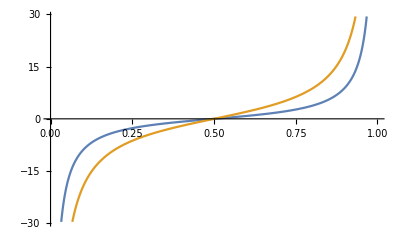

```mathematica
B[a_,L_,L1_]:=-a/L1+a/(L-L1);
B2[a_,L_,L1_]:=(-2×π×a)/L×Cot[(π×L1)/L];
Plot[{B[1,1,x],B2[1,1,x]},{x,0,1}]
```

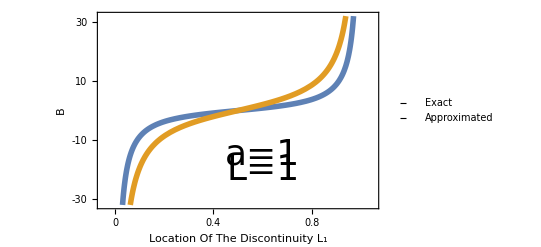

```mathematica
Plot[{B[1,1,x],B2[1,1,x]},{x,0,1},PlotStyle->{Thickness[0.01]}, Frame->{True, True, True, True},FrameTicks->{{{-30,-20,-10,0,10,20,30},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{-0.05,1.05},{-32,32}},FrameLabel->{{"B", None},{"Location Of The Discontinuity L_1", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"Exact","Approximated"},LegendMarkers->{{Graphics[Rectangle[{1,1},{10,2}]],80},{Graphics[Rectangle[{1,1},{10,2}]],80}}],{Left, Top}],Epilog->{Text[Style["a=1",Directive[Black,36]],{0.6,-15}],Text[Style["L=1",Directive[Black,36]],{0.6,-20}]}]
```